# Generate the Mean and Variance for the Maximum Energy of the spherical p-spin

This notebook generates the mean and variance of the maximum energy for the spherical p-spin model. This is done using theoretical work in https://arxiv.org/abs/1509.03098. Most of the notebook consists of defining constants listed in the paper. The functions “mean” and “variance” calculate the mean and variance for a given N assuming p=3. This could be easily generalized to any p.

```mathematica
γ[p_] = Sqrt[p / (p-1)]; (* Checked *)
Ω[x_] = Piecewise[{{x^2 / 4 - 1/2, 0 ≤ RealAbs[x] < 2}, {x^2 / 4 -1/2 - (RealAbs[x]/4 * Sqrt[x^2-4] -Log[Sqrt[x^2/4-1] + RealAbs[x]/2]), RealAbs[x]≥ 2}}]; (* Checked *)
Θ[p_, u_] = Piecewise[{{1/2 + 1/2 * Log[p-1] - u^2/2 + Ω[γ[p] u], u < 0}, {1/2 Log[p-1], u≥0}}]; (* Checked *)
```

For simplicity, the rest of the notebook I will assume p=3.

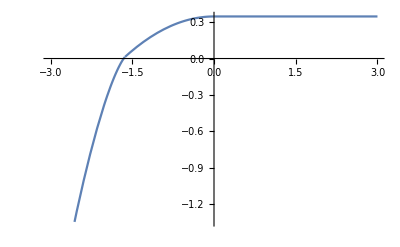

```mathematica
Plot[Θ[3, x], {x, -3, 3}]
```

```mathematica
(* Checked *)
Subscript[e, 0]=-x/.FindRoot[Θ[3, x], {x, -1.5}]
```

1.657

```mathematica
dervTheta[x_]= D[Θ[3, x], x];
```

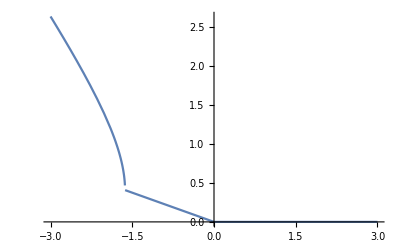

```mathematica
Plot[dervTheta[x], {x, -3, 3}]
```

```mathematica
Subscript[c, p]=dervTheta[-Subscript[e, 0]] (* Checked *)
```

0.625021

```mathematica
i=(1+(-1)^3)/2; (* Checked *)
```

```mathematica
h[x_]=(Abs[(x-1)/(x+1)]^(1/4) + Abs[(x+1) / (x-1)]^(1/4)); (*Checked*)
```

```mathematica
Subscript[k, 0]= 1/2 Subscript[e, 0]-1/Subscript[c, p]Log[(1+i)/(2Sqrt[2Pi]) * h[-1/2γ[3] Subscript[e, 0]]] (* Checked *)
```

1.30853

```mathematica
m[n_] = -Subscript[e, 0]n+ 1/2 * Log[n]/Subscript[c, p]+Subscript[k, 0] (* Changed the sign on the k to positive *)
```

1.30853-1.657 n+0.799973 Log[n]

```mathematica
β[n_] = 1/(Sqrt[n] Subscript[c, p]);
```

```mathematica
μ[n_] =- m[n]/Sqrt[n]-Log[Subscript[c, p]]/(Sqrt[n] Subscript[c, p])
```

0.751927/(√n)+(-1.30853+1.657 n-0.799973 Log[n])/(√n)

```mathematica
mean[n_] = μ[n]+EulerGamma β[n];
variance[n_] = Pi^2/6 *β[n]^2;
```

```mathematica
mean[n] //FullSimplify
```

(0.366915+1.657 n-0.799973 Log[n])/(√n)

```mathematica
variance[n]//FullSimplify
```

4.21075/n

```mathematica
meanTheory[n_] = 1/( Sqrt[1/2 / n] * (0.853 + 0.413 * Log[n] / n - 0.571 / n));
```

```mathematica
Series[meanTheory[n], {n,Infinity,1}] //FullSimplify
```

1.65793 √n+(1.10982-0.802725 Log[n]) √(1/n)+O[1/n]^(3/2)

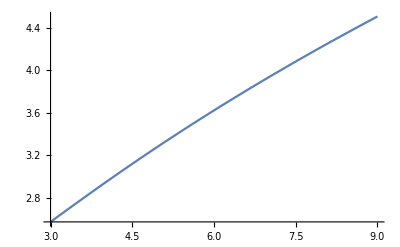

```mathematica
Plot[mean[x], {x, 3, 9}]
```

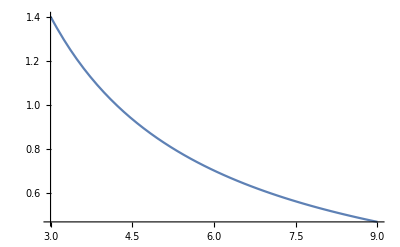

```mathematica
Plot[variance[x], {x, 3, 9}]
```

```mathematica
n = Range[3, 9];
```

```mathematica
meanVals = mean[n];
```

```mathematica
data= Transpose@{n, meanVals};
```

```mathematica
Export["pSpinTheoryMean.txt",data, "Table"];
```

```mathematica
varVals = variance[n];
```

```mathematica
dataVar = Transpose@{n, varVals};
```

```mathematica
Export["pSpinTheoryVariance.txt", dataVar, "Table"];
```